# Plot testing code

## Version: 1.2.5

```mathematica
" 
Mathematica-ported version of the data processing and plot generation code. Current implementation includes the core data extraction and plotting, more in-depth analysis will have to wait until I figure out how filtering works on Mathematica.
"
```

## Setup

### Directory setting

```mathematica
" 
Find file directory, then use that to navigate to data directory. Will work on any filesystem organized in accordance to current data organization protocol
"
```

```mathematica
currentDir=NotebookDirectory[];
SetDirectory[currentDir];
importdir="../../data/trajectories/";
exportdir="../../data/plots/mathematica/";
```

### File import

```mathematica
filename="n1b18x18VR2019110810data";(*"2020072013pooldata";*)
hdf5File=Import[ToString@Row@{importdir,filename,".hdf5"},"Data"];
Needs["ErrorBarPlots`"]
```

### Recording Parameters

```mathematica
" 
Parameters from experiment recording. Upgrade this later to automatically import the values from a params file to ensure human error doesn't mess up calculations
"
```

```mathematica
size=17.5;
framerate=10;
trajLen=18000;
boundary=2;
```

## Functions

### I. Position array

```mathematica
" There is a problem where there is missing data (NaN) and Mathematica fails to handle NaN because that's not a recognized object. For now, temporary patch is to simply average over previous subsequent values, but this will fail when multiple successive points are missing data entries. 
"
```

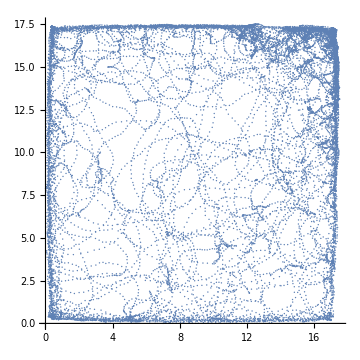

```mathematica
position={};
Module[{x,y,xholes,yholes},
Do[
dset=hdf5File⟦i⟧;
{x,y}=Transpose[dset⟦2;;2+trajLen,1;;2⟧];
Do[If[x⟦i⟧<2,x⟦i⟧=(x⟦i-1⟧+x⟦i-1⟧)/2],{i,1,Length[x]}];
Do[If[y⟦i⟧<2,y⟦i⟧=(y⟦i-1⟧+y⟦i-1⟧)/2],{i,1,Length[y]}];
xmax=Max[x]-Min[x];
ymax=Max[y]-Min[y];
x=((x-Min[x])size)/(Max[x]-Min[x]);
y=((y-Min[y])size)/(Max[y]-Min[y]);
AppendTo[position,Transpose[{x,y}]];
,{i,1,Length[hdf5File]}]];ListPlot[position,AspectRatio->1,ImageSize->Medium]
```

### II. Velocity array (+ III. Speed array)

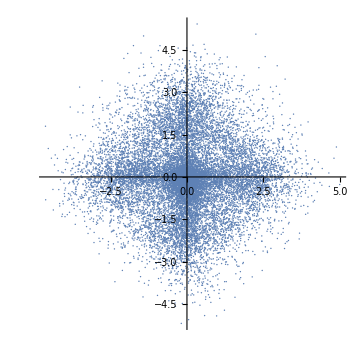

```mathematica
velocity={};
speed={};
Module[{pos,velx,vely,vel,spd},
Do[
pos=Transpose[position⟦i⟧];
velx=Differences[pos⟦1⟧] framerate;
vely=Differences[pos⟦2⟧]framerate;
vel=Transpose[{velx,vely}];
spd=Sqrt[vel⟦;;,1⟧^2+vel⟦;;,2⟧^2];
AppendTo[velocity,vel];
AppendTo[speed,spd];
,{i,1,Length[hdf5File]}]];ListPlot[velocity⟦1⟧,AspectRatio->1,ImageSize->Medium]
```

### III. Orientation array

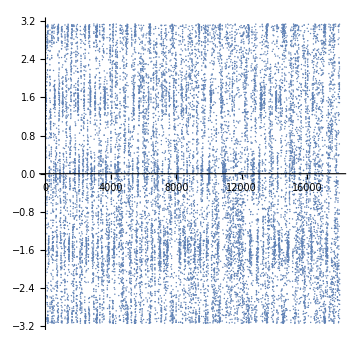

```mathematica
orientation={};
ct=0;
Module[{velx,vely,orr},
Do[
{velx,vely}=Transpose[velocity⟦i⟧];
orr=ArcTan[velx,vely]+π;
(*Do[
If[Abs[orr⟦k⟧-orr⟦k-1⟧]>π,
orr⟦k⟧=Mod[orr⟦k⟧-π,2.π]];
ct+=1;
,{k,2,Length[orr]}];*)
AppendTo[orientation,orr-π];
,{i,1,Length[hdf5File]}]];ListPlot[orientation⟦1⟧,AspectRatio->1,ImageSize->Medium]
```

### IV. Angular velocity array

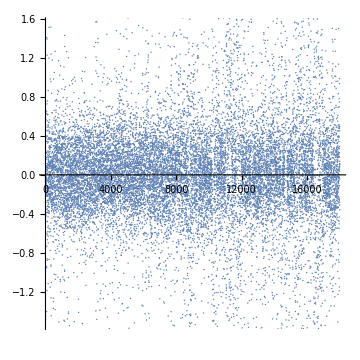

```mathematica
angularVelocity={};
Module[{orr,av},
Do[
orr=orientation⟦i⟧;
av=Mod[Differences[orr]+π,2.π]-π;
AppendTo[angularVelocity,av]
,{i,1,Length[hdf5File]}]];ListPlot[angularVelocity⟦1⟧,AspectRatio->1,ImageSize->Medium]
```

### IV. Acceleration array

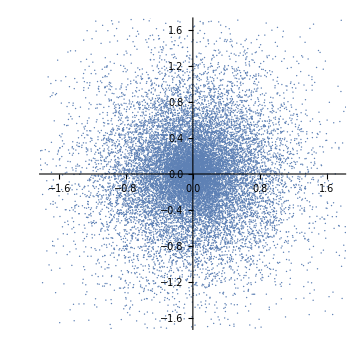

```mathematica
acceleration={};
Module[{velx,vely,accx,accy},
Do[
{velx,vely}=Transpose[velocity⟦i⟧];
accx=Differences[velx];
accy=Differences[vely];
AppendTo[acceleration,Transpose[{accx,accy}]];
,{i,1,Length[hdf5File]}]];ListPlot[acceleration⟦1⟧,AspectRatio->1,ImageSize->Medium]
```

## Analyses

### Symmetry check

```mathematica
" This Block adds up the values of Orientation and Angular velocity over datasets and timesteps; if distribution is indeed symmetric, the sum must evaluate to zero";
```

```mathematica
orrSum=Sum[orientation⟦i,j⟧,{i,1,Length[hdf5File]},{j,1,trajLen-1}]
```

-1331.31

```mathematica
avSum=Sum[angularVelocity⟦i,j⟧,{i,1,Length[hdf5File]},{j,1,trajLen-2}]
```

168.277

```mathematica
" Sums are very far from zero ";
```

### Data filtering by distance from boundary

```mathematica
boundaryMask={};
Module[{mask},
mask={};mask=Position[position⟦;;,2;;-2⟧,_?(((#⟦1⟧>boundary ∧#⟦2⟧>boundary)∧(#⟦1⟧<size-boundary∧#⟦2⟧<size-boundary))&),{2},Heads->False];
boundaryMask=mask;
]
positionF=position⟦#⟦1⟧,#⟦2⟧⟧&/@boundaryMask;
angularVelocityF=angularVelocity⟦#⟦1⟧,#⟦2⟧⟧&/@boundaryMask;Histogram3D[positionF]
```

-Graphics3D-

## Generate figures

### Angular velocity plots

```mathematica
(*
Valid variables: speed, orientation, angular velocity
*)
```

#### Generate plots

```mathematica
Module[
(* Set local parameters for plotting *)
{data=angularVelocity,
samplesize=0,
flatten=True,
axesLabel={"Orientation (rad)","Probability density"},
bincounts=20,
angularticks=True,
range, ticks, err, dist, hist, len, errors, binwidth, copy, temp},

(* Modify structure of data and set up plotting parameters *)
Do[
samplesize+=Length[data⟦i⟧]
,{i,1,Length[data]}];
If[samplesize==0,
samplesize=Length[data]];
If[flatten,data=Flatten[data]];
range={Min[data],Max[data]};
If[angularticks,
ticks={Range[-2π,2π,π/8],Automatic},
ticks=Automatic];
err={};
Do[
AppendTo[err,ErrorBar[1./(range⟦2⟧-range⟦1⟧),1/Sqrt[samplesize]]];
,{n,1,10}];

(* Generate basic plots using the configs *)
dist=SmoothKernelDistribution[data];
avdist=dist;
avHistogram=Histogram[data,bincounts,"PDF",AxesLabel->axesLabel,PlotRange->Full,ImageSize->Large,Ticks->ticks,GridLines->Automatic,PlotLabel->"Histogram of Angular Velocity folded in half"];
avPDF=Plot[PDF[dist,x],{x,0,π},PlotRange->Full,AxesLabel->axesLabel,ImageSize->Large,Ticks->ticks,PlotLabel->"Kernel distribution of Angular Velocity near center"];
avCDF=Plot[CDF[dist,x],{x,0,π},PlotRange->Full,AxesLabel->axesLabel,ImageSize->Large,Ticks->ticks,PlotLabel->"Kernel PDF of Angular Velocity near center"];

(* Generate histogrambins for further analysis *)
temp={};
hist=HistogramList[data,{π/bincounts},"PDF"];
len=Length[hist⟦1⟧];
errors={};
Do[
AppendTo[temp,(hist⟦1,i⟧+hist⟦1,i+1⟧)/2.];
binwidth=π/bincounts;
AppendTo[errors,ErrorBar[binwidth/2.,Sqrt[hist⟦2,i⟧(1-hist⟦2,i⟧binwidth)/(Length[data]binwidth)]]]
,{i,1,Length[hist⟦2⟧]}];
hist={temp,hist⟦2⟧};
copy=histᵀ;
hist=Partition[Riffle[histᵀ,errors],2];

(* Generate Error analysis and symmetry analysis plots *)
avErrorPlot=ErrorListPlot[hist,PlotRange->{{0,0.75},Full},AxesLabel->axesLabel,PlotLabel->"Histogram of Orientation (With error bars)",PlotStyle->PointSize[0]];(*mirror=[-copyᵀ⟦1⟧,Reverse[copyᵀ⟦2⟧];*)
avSym=ListPlot[{{ -copyᵀ⟦1⟧,copyᵀ⟦2⟧}ᵀ,copy},PlotRange->{{0,Automatic},Full},PlotLabel->"Left-Right comparison for angular velocity distribution",PlotLegends->{"Left","Right"},ImageSize->700,Ticks->ticks,AxesLabel->{"Angular velocity (rad/s)", "PDF"}];
];
```

#### Render plots

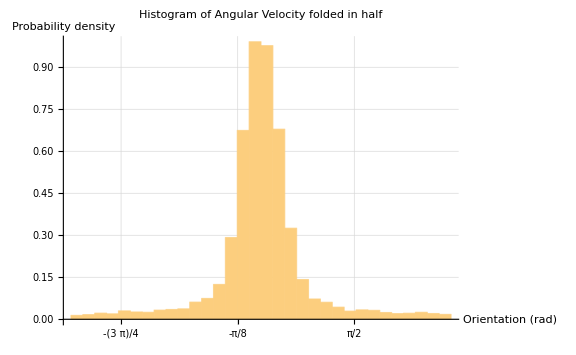

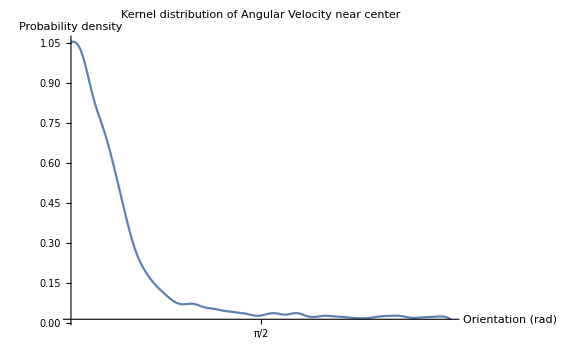

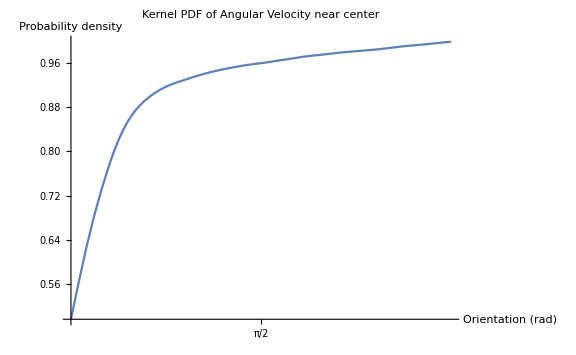

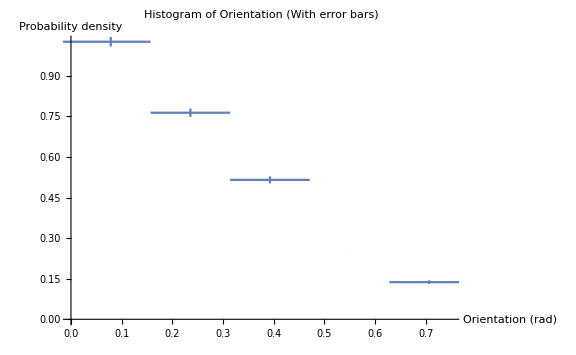

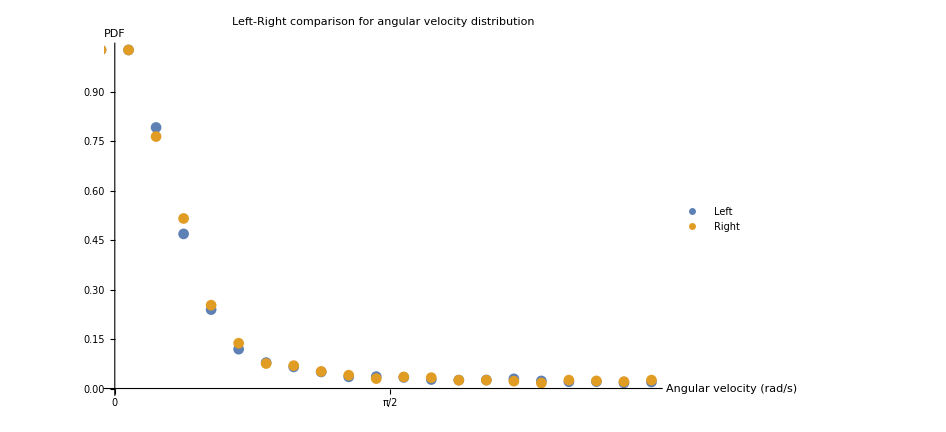

```mathematica
avHistogram
avPDF
avCDF
avErrorPlot
avSym
```

#### Export plots

```mathematica
Export[ToString@Row@{exportdir,"AngularvelocityHistogram.png"},avHistogram];
Export[ToString@Row@{exportdir,"AngularvelocityPDF.png"},avPDF];
Export[ToString@Row@{exportdir,"AngularvelocityCDF.png"},avCDF];
Export[ToString@Row@{exportdir,"AngularvelocityErrorPlot.png"},avErrorPlot];
Export[ToString@Row@{exportdir,"AngularvelocitySymmetrycheck.png"},avSym];
```

Export::nodir: Directory C:\Users\user\Desktop\Coding\ant\data\plots\mathematica\ does not exist.

Export::noopen: Cannot open ../../data/plots/mathematica/AngularvelocityHistogram.png.

Export::nodir: Directory C:\Users\user\Desktop\Coding\ant\data\plots\mathematica\ does not exist.

Export::noopen: Cannot open ../../data/plots/mathematica/AngularvelocityPDF.png.

Export::nodir: Directory C:\Users\user\Desktop\Coding\ant\data\plots\mathematica\ does not exist.

Export::noopen: Cannot open ../../data/plots/mathematica/AngularvelocityCDF.png.

Export::nodir: Directory C:\Users\user\Desktop\Coding\ant\data\plots\mathematica\ does not exist.

Export::noopen: Cannot open ../../data/plots/mathematica/AngularvelocityErrorPlot.png.

Export::nodir: Directory C:\Users\user\Desktop\Coding\ant\data\plots\mathematica\ does not exist.

Export::noopen: Cannot open ../../data/plots/mathematica/AngularvelocitySymmetrycheck.png.

### Orientation plots

#### Generate plots

```mathematica
Module[
(* Set local parameters for plotting *)
{data=orientation,
samplesize=0,
flatten=True,
axesLabel={"Orientation (rad)","Probability density"},
bincounts=20,
angularticks=True,
range, ticks, err, dist, hist, len, errors, binwidth, copy, temp},

(* Modify structure of data and set up plotting parameters *)
Do[
samplesize+=Length[data⟦i⟧]
,{i,1,Length[data]}];
If[samplesize==0,
samplesize=Length[data]];
If[flatten,data=Flatten[data]];
range={Min[data],Max[data]};
If[angularticks,
ticks={Range[-2π,2π,π/8],Automatic},
ticks=Automatic];
err={};
Do[
AppendTo[err,ErrorBar[1./(range⟦2⟧-range⟦1⟧),1/Sqrt[samplesize]]];
,{n,1,10}];

(* Generate basic plots using the configs *)
dist=SmoothKernelDistribution[data];
orientationHistogram=Histogram[data,bincounts,"PDF",AxesLabel->axesLabel,PlotRange->Full,ImageSize->Large,Ticks->ticks,GridLines->Automatic,PlotLabel->"Histogram of Angular Velocity folded in half"];
orientationPDF=Plot[PDF[dist,x],{x,0,π},PlotRange->Full,AxesLabel->axesLabel,ImageSize->Large,Ticks->ticks,PlotLabel->"Kernel distribution of Angular Velocity near center"];
orientationCDF=Plot[CDF[dist,x],{x,0,π},PlotRange->Full,AxesLabel->axesLabel,ImageSize->Large,Ticks->ticks,PlotLabel->"Kernel PDF of Angular Velocity near center"];

(* Generate histogrambins for further analysis *)
temp={};
hist=HistogramList[data,{π/bincounts},"PDF"];
len=Length[hist⟦1⟧];
errors={};
Do[
AppendTo[temp,(hist⟦1,i⟧+hist⟦1,i+1⟧)/2.];
binwidth=π/bincounts;
AppendTo[errors,ErrorBar[binwidth/2.,Sqrt[hist⟦2,i⟧(1-hist⟦2,i⟧binwidth)/(Length[data]binwidth)]]]
,{i,1,Length[hist⟦2⟧]}];
hist={temp,hist⟦2⟧};
copy=histᵀ;
hist=Partition[Riffle[histᵀ,errors],2];

(* Generate Error analysis and symmetry analysis plots *)
orientationErrorPlot=ErrorListPlot[hist,PlotRange->{{0,0.75},Full},AxesLabel->axesLabel,PlotLabel->"Histogram of Orientation (With error bars)",PlotStyle->PointSize[0]];(*mirror=[-copyᵀ⟦1⟧,Reverse[copyᵀ⟦2⟧];*)
orientationSym=ListPlot[Table[Block[{a=Select[copy,-π+((i-1) π)/4≤#⟦1⟧≤-π+(π i)/4&]},
({(-1)^(i+1)(#⟦1⟧-(i π)/4+(9π)/8)+π/8,#⟦2⟧}&/@aᵀ)ᵀ
],{i,1,8}],AxesLabel->{"Angle (rad)", "PDF"},Ticks->ticks,ImageSize->Large,PlotLabel->"Orientation symmetry check"];
oriCentralMoments={CentralMoment[data,3],CentralMoment[data,2],CentralMoment[data,4]};
orientationSkew=CentralMoment[data,3]/(CentralMoment[data,2])^(3/2) (* Used 2nd moment here because mean is zero; this division is needed because then scale factor affects value of moments *)
];
```

#### Render plots

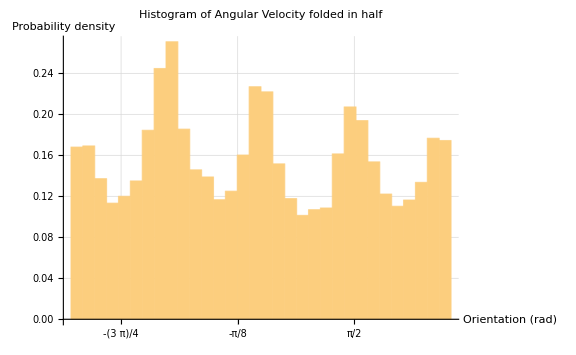

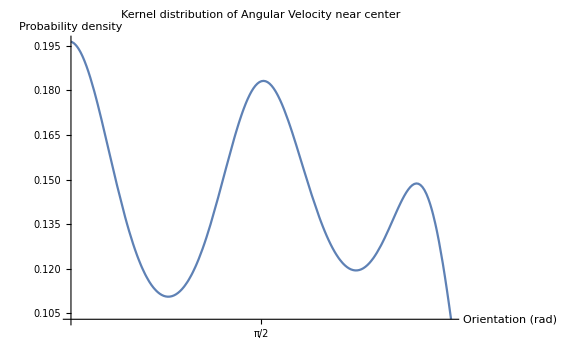

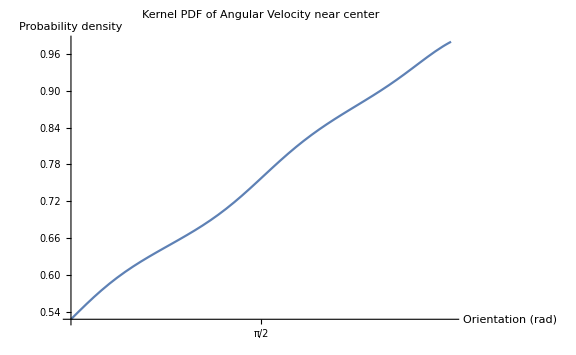

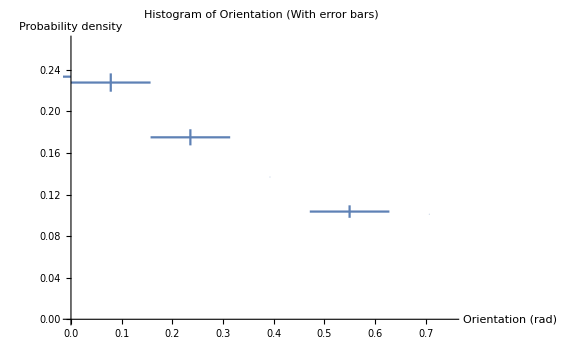

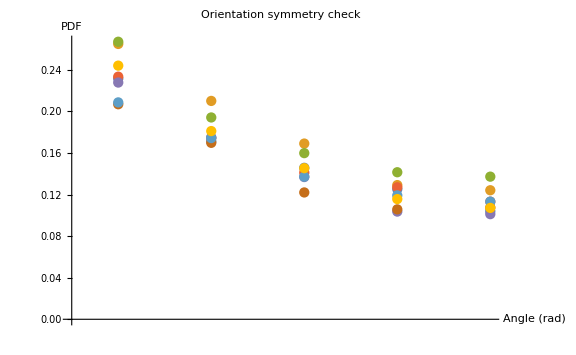

```mathematica
orientationHistogram
orientationPDF
orientationCDF
orientationErrorPlot
orientationSym
```

#### Export plots

```mathematica
Export[ToString@Row@{exportdir,"OrientationHistogram.png"},orientationHistogram];
Export[ToString@Row@{exportdir,"OrientationPDF.png"},orientationPDF];
Export[ToString@Row@{exportdir,"OrientationCDF.png"},orientationCDF];
Export[ToString@Row@{exportdir,"OrientationErrorPlot.png"},orientationErrorPlot];
Export[ToString@Row@{exportdir,"OrientationSymmetrycheck.png"},orientationSym];
```

Export::nodir: Directory C:\Users\user\Desktop\Coding\ant\data\plots\mathematica\ does not exist.

Export::noopen: Cannot open ../../data/plots/mathematica/OrientationHistogram.png.

Export::nodir: Directory C:\Users\user\Desktop\Coding\ant\data\plots\mathematica\ does not exist.

Export::noopen: Cannot open ../../data/plots/mathematica/OrientationPDF.png.

Export::nodir: Directory C:\Users\user\Desktop\Coding\ant\data\plots\mathematica\ does not exist.

Export::noopen: Cannot open ../../data/plots/mathematica/OrientationCDF.png.

Export::nodir: Directory C:\Users\user\Desktop\Coding\ant\data\plots\mathematica\ does not exist.

Export::noopen: Cannot open ../../data/plots/mathematica/OrientationErrorPlot.png.

Export::nodir: Directory C:\Users\user\Desktop\Coding\ant\data\plots\mathematica\ does not exist.

Export::noopen: Cannot open ../../data/plots/mathematica/OrientationSymmetrycheck.png.

#### Orientation symmetry check

```mathematica
wrap2=data;
```

```mathematica
wraplength=Length[wrap2]/8;
wrap=wrap2⟦wraplength+1;;⟧;
wrap=AppendTo[wrap,wrap2⟦;;wraplength⟧];
wrap2=Flatten[wrap];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol::string: String expected at position 1 in Symbol[Symbol[]].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
dimensionfree=CentralMoment[wrap2,3]/(CentralMoment[wrap2,2])^(3/2)
wrap2⟦1⟧
```

CentralMoment::arg1: The first argument Symbol[] is expected to be a vector, a matrix, or a distribution.

CentralMoment[Symbol[],3]/CentralMoment[Symbol[],2]^(3/2)

Part::partw: Part 1 of Symbol[] does not exist.

Symbol[]⟦1⟧

```mathematica
Dimensions[wrap2]
```

{0}

```mathematica
{0.053,0.053,0.052,0.48,0.45,0.72,0.88,0.91};
```

```mathematica
(* For oreintation, do the central moment calculation 4 times over 2 peaks and 2 troughs, make sure to wrap data around *)
```

```mathematica
data⟦2⟧
```

Part::partd: Part specification data⟦2⟧ is longer than depth of object.

data⟦2⟧

```mathematica
Dimensions[wrap]
```

{1,0}

### Speed plots

#### Generate plots

```mathematica
Module[
(* Set local parameters for plotting *)
{data=speed,
samplesize=0,
flatten=True,
axesLabel={"Speed (pixels/s)","Probability density"},
bincounts=50,
angularticks=False,
range, ticks, err, dist, hist, len, errors, binwidth, copy, temp},

(* Modify structure of data and set up plotting parameters *)
Do[
samplesize+=Length[data⟦i⟧]
,{i,1,Length[data]}];
If[samplesize==0,
samplesize=Length[data]];
If[flatten,data=Flatten[data]];
range={Min[data],Max[data]};
If[angularticks,
ticks={Range[-2π,2π,π/8],Automatic},
ticks=Automatic];
err={};
Do[
AppendTo[err,ErrorBar[1./(range⟦2⟧-range⟦1⟧),1/Sqrt[samplesize]]];
,{n,1,10}];

(* Generate basic plots using the configs *)
dist=SmoothKernelDistribution[data];
speeddist=dist;
speedHistogram=Histogram[data,bincounts,"PDF",AxesLabel->axesLabel,PlotRange->{{0,Max[data]/2},Full},ImageSize->Large,Ticks->ticks,GridLines->Automatic,PlotLabel->"Histogram of Angular Velocity folded in half"];
speedPDF=Plot[PDF[dist,x],{x,0,Max[data]/2.},PlotRange->Full,AxesLabel->axesLabel,ImageSize->Large,Ticks->ticks,PlotLabel->"Kernel distribution of Angular Velocity near center"];
speedCDF=Plot[CDF[dist,x],{x,0,Max[data]/2.},PlotRange->Full,AxesLabel->axesLabel,ImageSize->Large,Ticks->ticks,PlotLabel->"Kernel PDF of Angular Velocity near center"];

(* Generate histogrambins for further analysis *)
temp={};
hist=HistogramList[data,{π/bincounts},"PDF"];
len=Length[hist⟦1⟧];
errors={};
Do[
AppendTo[temp,(hist⟦1,i⟧+hist⟦1,i+1⟧)/2.];
binwidth=π/bincounts;
AppendTo[errors,ErrorBar[binwidth/2.,Sqrt[hist⟦2,i⟧(1-hist⟦2,i⟧binwidth)/(Length[data]binwidth)]]]
,{i,1,Length[hist⟦2⟧]}];
hist={temp,hist⟦2⟧};
copy=histᵀ;
hist=Partition[Riffle[histᵀ,errors],2];

(* Generate Error analysis and symmetry analysis plots *)
speedErrorPlot=ErrorListPlot[hist,PlotRange->{{0,Max[data]/2.},Full},AxesLabel->axesLabel,PlotLabel->"Histogram of Orientation (With error bars)",PlotStyle->PointSize[0]];
speedCentralMoments={CentralMoment[data,3],CentralMoment[data,2],CentralMoment[data,4]};
speedSkew=CentralMoment[data,3]/(CentralMoment[data,2])^(3/2) (* Used 2nd moment here because mean is zero; this division is needed because then scale factor affects value of moments *)
];
```

#### Render plots

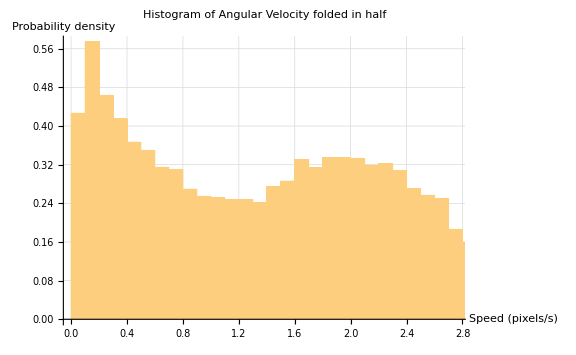

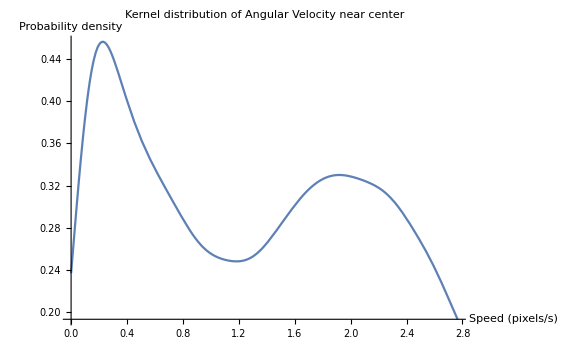

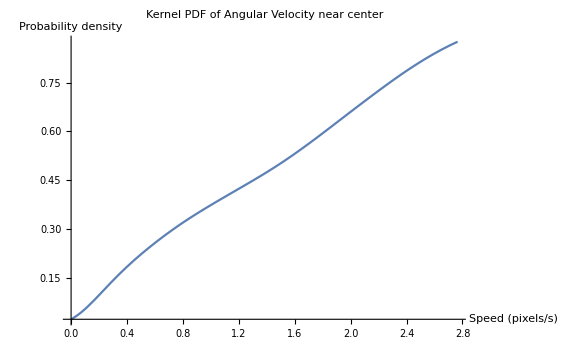

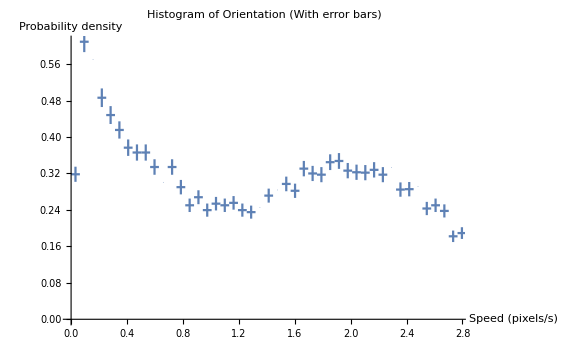

0.386886

```mathematica
speedHistogram
speedPDF
speedCDF
speedErrorPlot
speedSkew
```

#### Export plots

```mathematica
Export[ToString@Row@{exportdir,"SpeedHistogram.png"},speedHistogram];
Export[ToString@Row@{exportdir,"SpeedPDF.png"},speedPDF];
Export[ToString@Row@{exportdir,"SpeedCDF.png"},speedCDF];
Export[ToString@Row@{exportdir,"SpeedErrorPlot.png"},speedErrorPlot];
```

Export::nodir: Directory C:\Users\user\Desktop\Coding\ant\data\plots\mathematica\ does not exist.

Export::noopen: Cannot open ../../data/plots/mathematica/SpeedHistogram.png.

Export::nodir: Directory C:\Users\user\Desktop\Coding\ant\data\plots\mathematica\ does not exist.

Export::noopen: Cannot open ../../data/plots/mathematica/SpeedPDF.png.

Export::nodir: Directory C:\Users\user\Desktop\Coding\ant\data\plots\mathematica\ does not exist.

Export::noopen: Cannot open ../../data/plots/mathematica/SpeedCDF.png.

Export::nodir: Directory C:\Users\user\Desktop\Coding\ant\data\plots\mathematica\ does not exist.

Export::noopen: Cannot open ../../data/plots/mathematica/SpeedErrorPlot.png.

### 3D-Histogram

```mathematica
" Valid variables: Position, velocity, acceleration ";
```

#### Plot config

```mathematica
data3d=position;
flatten=True;
axesLabel={"x (cm)","y (cm)","Frequency"};
angularticks=False;
bincounts=8;
```

#### Plot generation

-Graphics3D-

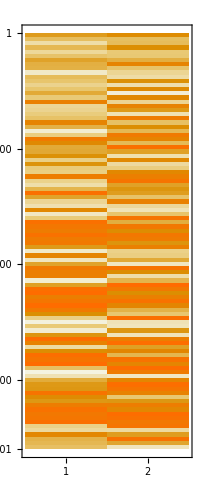

```mathematica
If[flatten,data3d=Flatten[data3d,1];flatten=False];
If[angularticks,
ticks={Range[-2π,2π,π/4],Automatic},
ticks=Automatic];
Histogram3D[data3d,{bincounts,bincounts},AxesLabel->axesLabel,PlotRange->{{Min[data3d],Max[data3d]},{Min[data3d],Max[data3d]},Automatic},ImageSize->Large,Ticks->ticks]
MatrixPlot[data3d]
```

#### Polar plot

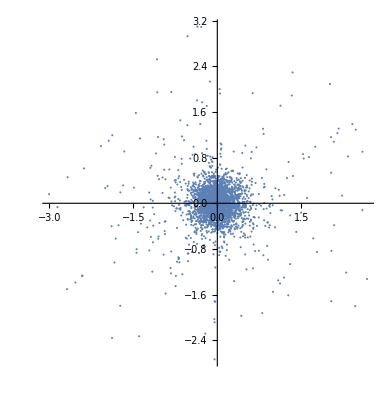

```mathematica
ListPolarPlot[angularVelocityF]
```

```mathematica
1.copy
```

1. copy

```mathematica
maxScale=1.1;
angleDivisions=bincounts;
dAng=(2. π)/(angleDivisions+1);
ccopy={copyᵀ⟦1⟧,copyᵀ⟦2⟧}ᵀ;
ListPolarPlot[{{0,maxScale}},PolarAxes->True,PolarGridLines->Automatic,PolarTicks->{"Radians",Automatic},PlotStyle->{None},Epilog->{Opacity[0.7],Blue,Table[Disk[{0,0}, ccopyᵀ⟦2,ang⟧,{ccopyᵀ⟦1,ang⟧-dAng/2.,ccopyᵀ⟦1,ang⟧+dAng/2.}],{ang,1,angleDivisions}]},PlotLabel->"Polar histogram of angular velocity in linear scales\n"]
```

Part::partw: Part 2 of Transpose[copy] does not exist.

Transpose::nmtx: The first two levels of {copy,Transpose[copy]⟦2⟧} cannot be transposed.

Part::partw: Part 2 of Transpose[Transpose[{copy,Transpose[copy]⟦2⟧}]] does not exist.

Part::partw: Part 2 of Transpose[{copy,Transpose[copy]⟦2⟧}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
1.ccopy⟦angleDivisions+2⟧
```

Part::partw: Part 10 of Transpose[{copy,Transpose[copy]⟦2⟧}] does not exist.

1. Transpose[{copy,Transpose[copy]⟦2⟧}]⟦10⟧

```mathematica
SectorChart[copy,PolarGridLines->Automatic,PolarTicks->{Automatic,None},PolarAxes->{True,False},SectorOrigin->0]
```

SectorChart::ldata: copy is not a valid dataset or list of datasets.

General::stop: Further output of SectorChart::ldata will be suppressed during this calculation.

SectorChart[copy,PolarGridLines→Automatic,PolarTicks→{Automatic,None},PolarAxes→{True,False},SectorOrigin→0]

```mathematica
Dimensions[hist]
```

{}

```mathematica
copy⟦1⟧
```

Part::partd: Part specification copy⟦1⟧ is longer than depth of object.

copy⟦1⟧

```mathematica
bb=HistogramList[dd];
```

HistogramList::ldata: dd is not a valid dataset or list of datasets.

```mathematica
Dimensions[bb⟦2⟧]
```

Part::partw: Part 2 of HistogramList[dd] does not exist.

{2}

```mathematica
MatrixPlot@bb
```

MatrixPlot::mat0: Argument HistogramList[dd] at position 1 is not a matrix.

MatrixPlot[HistogramList[dd]]

```mathematica
dd=data3dᵀ⟦1⟧;
```

```mathematica
Dimensions[bb⟦⟧]
```

{2}

```mathematica
HistogramList
```

HistogramList

```mathematica
Dimensions[data3d]
```

{18001,2}

```mathematica
binsize=17.5/bincounts+0.01;
thing =BinCounts[data3d,binsize,binsize];
Dimensions[thing]
```

{9,9}

```mathematica
thing=Drop[thing,1];
Do[
thing⟦j⟧=Drop[thing⟦j⟧,1]
,{j,1,Length[thing]}]
```

```mathematica
thing=thing/Length[data3d];
```

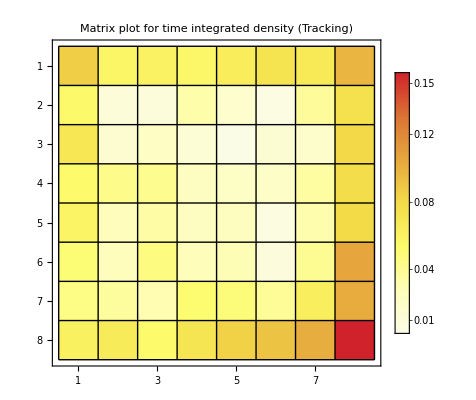

```mathematica
out=Show[MatrixPlot[thing,PlotLegends->Automatic,ColorFunction->"TemperatureMap",Mesh->True,MeshStyle->Thin,PlotLabel->"Matrix plot for time integrated density (Tracking)"]]
```

```mathematica
Export["outtr.png",out]
```

outtr.png

```mathematica
thing⟦1⟧=1
```

1

```mathematica
Max[data3d]
```

17.5

```mathematica
Total@Total@thing
```

158898/18001

## Model fitting

### Gaussian

```mathematica
gaus={a Exp[(-(x)^2)/(2 b^2)],a>0,b>0};
nlm=NonlinearModelFit[copy, gaus, {a,b}, x];
```

```mathematica
Plot[nlm[x],{x,-π,π},PlotRange->Full]
```

```mathematica
nlm
```

```mathematica
s=Sqrt[(1/2)/1.59468]
```

```mathematica
Histogram@Flatten[orientation]
```

```mathematica
Min[orientation]
```

## Using syemmetry to fold data

### Orientation

```mathematica
rescaled=Flatten@Table[Block[{a=Select[data,-π+((i-1) π)/4≤#≤-π+(π i)/4&]},
((-1)^(i+1)(#-(i π)/4+(9π)/8)+π/8)&/@a
],{i,1,8}];
```

```mathematica
Histogram@rescaled
```

### Angular velocity

```mathematica
angularrescaled=Abs[data];
```

```mathematica
Histogram@angularrescaled
```

```mathematica
hist
```

```mathematica
Length[data]
```

```mathematica
hist⟦1⟧
```

```mathematica
hist=HistogramList[data,{(1.π)/bincounts},"PDF"] binwidth
```

```mathematica
meh={1,22,3,4,5};
```

```mathematica
meh⟦3;;5⟧
```

```mathematica
beh=meh⟦4;;⟧;
beh=AppendTo[beh,meh⟦;;3⟧];
meh=Flatten[beh]
```

```mathematica
changev=Norm[acceleration⟦1,#⟧]&/@Range@Length@acceleration⟦1⟧;
```

```mathematica
Histogram@changev
```

## Diffs

```mathematica
diffs=framerate(speed⟦1,2;;⟧-speed⟦1,;;-2⟧);
```

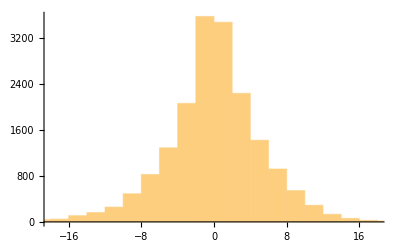

```mathematica
Histogram@diffs
```

```mathematica
diffsfn=SmoothKernelDistribution[diffs]
```

DataDistribution[…]

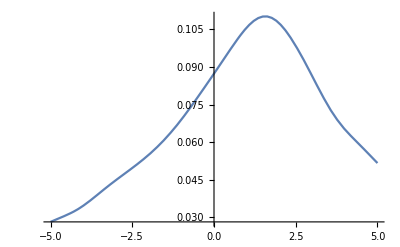

```mathematica
Plot[PDF[diffsfn,1.51624-x],{x,-5,5},PlotRange->All]
```

```mathematica
Mean@speed⟦1⟧
```

1.51624

```mathematica
angularacc=angularVelocity⟦1,2;;⟧-angularVelocity⟦1,;;-2⟧;
```

```mathematica
angularaccdist=SmoothKernelDistribution[angularacc]
```

DataDistribution[…]

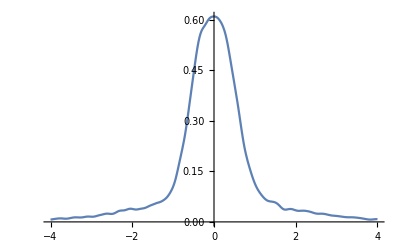

```mathematica
Plot[PDF[angularaccdist,x],{x,-4,4}]
```

```mathematica
angularacc⟦2⟧
```

0.116411